```mathematica
QE
```

2.07215×10^-6

```mathematica
QE/kb/10^(11)
```

0.15008

```mathematica
(* equation 26 in Kaz 2002 paper with QE left in equation *)
```

```mathematica
myQE=QE
funmue=(rhob/mp*Exp[(myQE-mue)/(kb*T)]-(1/(3*Pi^2)*(mue/(hbar*c))^3))//.{mue->etae*kb*T}
eq1=FullSimplify[funmue==0]
```

2.07215×10^-6

5.97864×10^23 ⅇ^((7.2427×10^15 (2.07215×10^-6-1.3807×10^-16 etae T))/T) rhob-2.8131 etae^3 T^3

1. etae^3 T^3==2.12528×10^23 ⅇ^(-1. etae+(1.5008×10^10)/T) rhob

```mathematica
npratio=Exp[-(QE-mue)/(kb*T)]//.{T->10^4,mue->etae*kb*T,etae->10^5}
```

1.27644117×10^-608359

```mathematica
1/ergPmev*kb
```

```mathematica
EN=1
EN*(ergPmev)^3/(hbar*c)^3
```

1

1.30149×10^32

```mathematica
T=10^4
rhob=10^4
```

10000

0.511

1.29

1.3014×10^32

1.16041×10^10

8.61764×10^-7

1.49693×10^6

5.97452×10^33

10000

592968.

x^2/(1+ⅇ^(-9054+√(3.51611×10^11+x^2)))

(8.4393×10^12 x^2)/(1+ⅇ^(-9054+√(3.51611×10^11+x^2)))

```mathematica
(* TIMMES EOS n_e *)
xconst=8*Pi*Sqrt[2]*(me/h)^3*c^3
mecc=me*c^2
beta=kb*T/mecc
beta12=Sqrt[beta]
beta32=beta*beta12
(*eta=6.016*10^5*)
eta=9054
fd[x_,dk_,theta_,eta_]:=x^dk*Sqrt[1+1/2*x*theta]/(Exp[x-eta]+1)
f12=NIntegrate[fd[x,0.5,beta,eta],{x,0,Infinity}]
f32=NIntegrate[fd[x,1.5,beta,eta],{x,0,Infinity}]
zz=xconst*beta32
yy=f12+beta*f32
necgs=zz*yy
```

2.48837×10^30

8.1871×10^-7

1.68643×10^-6

0.00129863

2.19005×10^-9

9054

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {10920.4}. NIntegrate obtained 580196. and 26264.7 for the integral and error estimates.

580196.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {10920.4}. NIntegrate obtained 3.16861×10^9 and 2.38777×10^8 for the integral and error estimates.

3.16861×10^9

5.44964×10^21

585540.

3.19098×10^27

```mathematica
g=2
lambda=h/(2*Pi*me*kb*T)^(1/2)
eta=9054
z=Exp[eta]
n=3/2
nbook=g/lambda^3*NIntegrate[x^(n-1)/(z^(-1)*Exp[x]+1),{x,0,Infinity}]/Gamma[n]
```

2

7.45371×10^-8

9054

ⅇ^9054

3/2

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {10920.4}. NIntegrate obtained 578866. and 26164.6 for the integral and error estimates.

3.15461×10^27

```mathematica
beta=1/(kb*T)
etae=9054
nbook2=1*(1/(2*Pi^2))*(2*me/hbar^2)^(3/2)*NIntegrate[ep^(1/2)/(Exp[beta*ep-etae]+1),{ep,0,Infinity}]
```

7.2427×10^11

9054

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ep near {ep} = {1.14591×10^-8}. NIntegrate obtained 9.31592×10^-13 and 3.93719×10^-14 for the integral and error estimates.

3.12928×10^27

```mathematica
beta=1/(kb*T)
etae=5.937*10^5
nbook2=1*(1/(2*Pi^2))*(2*me/hbar^2)^(3/2)*NIntegrate[ep^(1/2)/(Exp[beta*ep-etae]+1),{ep,me*c^2,Infinity}]
```

7.2427×10^11

593700.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ep near {ep} = {8.19704×10^-7}. NIntegrate obtained 9.07522×10^-13 and 1.34039×10^-14 for the integral and error estimates.

3.04843×10^27

```mathematica
beta=1/(kb*T)
etae=9054+me*c^2*beta
nbook2=1*(1/(2*Pi^2))*(2*me/hbar^2)^(3/2)*NIntegrate[ep^(1/2)/(Exp[beta*ep-etae]+1),{ep,me*c^2,Infinity}]
```

7.2427×10^11

602022.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ep near {ep} = {8.3017×10^-7}. NIntegrate obtained 1.13533×10^-11 and 3.21925×10^-13 for the integral and error estimates.

3.81366×10^28

```mathematica
beta=1/(kb*T)
etae=5.937*10^5
myep=Sqrt[p^2*c^2+me^2*c^4]
depdp=D[myep,p]
integrand=depdp*ep^(1/2)/(Exp[beta*ep-etae]+1)//.{ep->myep}
nbooktrans=1*(1/(2*Pi^2))*(2*me/hbar^2)^(3/2)*NIntegrate[integrand,{p,0,10*me*c}]
```

7.2427×10^11

593700.

√(6.70287×10^-13+8.98755×10^20 p^2)

(8.98755×10^20 p)/(√(6.70287×10^-13+8.98755×10^20 p^2))

(8.98755×10^20 p)/((1+ⅇ^(-593700.+7.2427×10^11 √(6.70287×10^-13+8.98755×10^20 p^2))) (6.70287×10^-13+8.98755×10^20 p^2)^(1/4))

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {1.59582×10^-18}. NIntegrate obtained 9.1644×10^-13 and 3.0954×10^-15 for the integral and error estimates.

3.07839×10^27

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.501431}. NIntegrate obtained 0. and 0. for the integral and error estimates.

0.

```mathematica
(* Kaz *)
Clear[etae];
memev=0.511
Qmev=1.29
mev3tocc=1.3014*10^(32)
mev2K=1.16041*10^(10)
tmev=T/mev2K
Qtilde=Qmev/tmev
A0=10^(10)/mb
Erat=(me*c^2)/(kb*T)
neleden=x^2/(Exp[Sqrt[x^2+Erat^2]-etae]+1)
fun=(1/hbar^3/Pi^2/c^3)*(kb*T)^3*neleden
Print["etae"];
myetae=6.016*10^5
(*myetae=9054*)
Log[10,myetae]
const={etae->myetae}
neledennum=neleden//.const
nelefake=neledennum//.{x->myetae}
nele=NIntegrate[neledennum,{x,0,10^(10)}]
neleshort=NIntegrate[neledennum,{x,10^(5),10^(6)}]
Print["ne_MeV"];
nelemev=nele*tmev^3/Pi^2
Print["ne_cgs"];
nelecgs=nele*(1/hbar^3/Pi^2/c^3)*(kb*T)^3
Print["nefake_cgs"];
nelefakecgs=nelefake*(1/hbar^3/Pi^2/c^3)*(kb*T)^3
Print["neshort_cgs"];
neleshortcgs=neleshort*(1/hbar^3/Pi^2/c^3)*(kb*T)^3
ZBAR=0.5037
rhob=10^4
LHS=nelecgs
RHS=rhob/10^(10)*A0*ZBAR
ferror=LHS-RHS
error=(LHS-RHS)/(Abs[LHS]+Abs[RHS])
```

0.511

1.29

1.3014×10^32

1.16041×10^10

8.61764×10^-7

1.49693×10^6

5.97452×10^33

592968.

x^2/(1+ⅇ^(-etae+√(3.51611×10^11+x^2)))

(8.4393×10^12 x^2)/(1+ⅇ^(-etae+√(3.51611×10^11+x^2)))

etae

601600.

5.77931

{etae→601600.}

x^2/(1+ⅇ^(-601600.+√(3.51611×10^11+x^2)))

4.91824769577239×10^-105570

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {90502.4}. NIntegrate obtained 3.5633×10^14 and 4.15475×10^13 for the integral and error estimates.

3.5633×10^14

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {100748.6989076521430206412333063781261444091796875}. NIntegrate obtained 1.45963×10^13 and 1.42721×10^12 for the integral and error estimates.

1.45963×10^13

ne_MeV

0.0000231056

ne_cgs

3.00717×10^27

nefake_cgs

4.15065830456906×10^-105557

neshort_cgs

1.23182×10^26

0.5037

10000

3.00717×10^27

3.00937×10^27

-2.19125×10^24

-0.000364205

```mathematica
(* See kazlike_crazy_ne_distributionissue.nb instead *)
(*
(*etae=6.016*10^5*)
etae=5.937*10^5
(*etae=9054*)
fact=p*(p^2*c^2/(me^2*c^4)+1)^(1/4)
dpdx=D[x*kb*T/c,x]
integrand=FullSimplify[dpdx*p^2/(fact*Exp[Sqrt[(p^2*c^2+me^2*c^4)/(kb*T)]-etae]+1)//.{p->x*kb*T/c}]
nkazcrazy=1/Pi^2*1/hbar^3*2^(1/2)*me/c*NIntegrate[integrand,{x,0,Infinity},WorkingPrecision->40]
*)
```

593700.

p (1+1.34085×10^33 p^2)^(1/4)

4.60552×10^-23

(4.2047659472637×10^257773 x^2)/(4.304333971×10^257840+4.60552×10^-23 ⅇ^(851041. √(6.70287×10^-13+1.90633×10^-24 x^2)) x (1.+2.84406×10^-12 x^2)^(1/4))

NIntegrate::precw: The precision of the argument function (4.2047659472637×10^257773\ x^2/4.304333971×10^257840 + 4.60552×10^-23\ ⅇ^« 1 »\ x\ (« 1 »)^1/4) is less than WorkingPrecision (40.).

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.093561654426143898807409137737082051806×10^10}. NIntegrate obtained 5.475290757024768904830466330413495185585×10^-33 and 3.781436613343052636734996291369362554595×10^-33 for the integral and error estimates.

2.03264×10^10

General::ovfl: Overflow occurred in computation.

General::stop: Further output of General :: "ovfl" will be suppressed during this calculation.

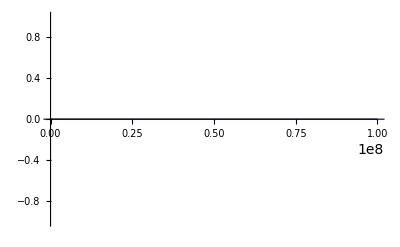

```mathematica
Plot[integrand,{p,0,etae}]
```

```mathematica
nelecode=2.9872577*10^(27)
nelecgs/nelecode
```

2.98726×10^27

1.00667

```mathematica
RHS
```

2.98726×10^27

```mathematica
Clear[GaussianQuadratureWeights]
```

Clear::wrsym: Symbol GaussianQuadratureWeights is Protected.

```mathematica
<<NumericalDifferentialEquationAnalysis`
```

```mathematica
gauss=GaussianQuadratureWeights[6,-1,1,30]
```

{{-0.9324695142031520278123015545,0.1713244923791703450402961422},{-0.661209386466264513661399595,0.3607615730481386075698335138},{-0.238619186083196908630501722,0.467913934572691047389870344},{0.238619186083196908630501722,0.467913934572691047389870344},{0.661209386466264513661399595,0.3607615730481386075698335138},{0.932469514203152027812301554,0.1713244923791703450402961422}}

```mathematica
Transpose[gauss][[1]]
```

{-0.9324695142031520278123015545,-0.661209386466264513661399595,-0.238619186083196908630501722,0.238619186083196908630501722,0.661209386466264513661399595,0.932469514203152027812301554}

```mathematica
Transpose[gauss][[2]]
```

{0.1713244923791703450402961422,0.3607615730481386075698335138,0.467913934572691047389870344,0.467913934572691047389870344,0.3607615730481386075698335138,0.1713244923791703450402961422}

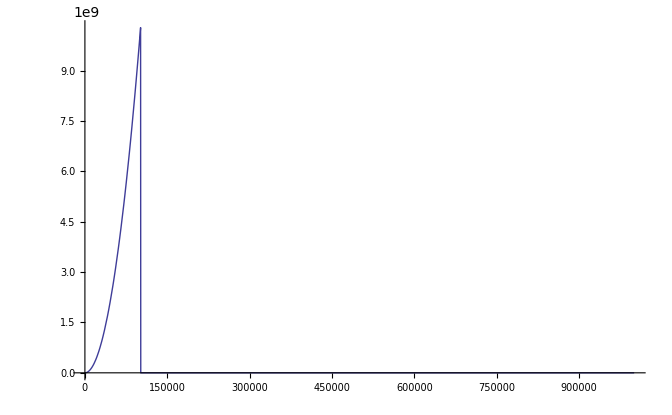

```mathematica
Plot[neledennum,{x,0,10^6}]
```

```mathematica
NUM=200;
NUMITER=50;
(*lTtable=Table[5.+i*(12-5)/(NUM-1),{i,0,NUM-1}];*)
lrhobtable=Table[2.+(i-1)*(15-2)/NUM,{i,1,NUM}];
etaetable=Table[0*i,{i,1,NUM}];
Clear[rhob,RHS,LHS,myetae,fundiff,fun,T]

T=10^4
A0=10^(10)/mb
Erat=(me*c^2)/(kb*T)
fun[etae_]:=(1/hbar^3/Pi^2/c^3)*(kb*T)^3*x^2/(Exp[Sqrt[x^2+Erat^2]-etae]+1)
```

10000

5.97452×10^33

592968.

```mathematica
LHS[etae_]:=NIntegrate[fun[etae],{x,0,etae}];
RHS:=rhob/10^(10)*A0*.5037;
fundiff[etae_]:=LHS[etae]-RHS;
(*Print["Before loop1"];*)
For[i=1,i<=NUM,
rhob=10^(lrhobtable[[i]]);
(*Print["rhob=",rhob];*)
etaemin=10^(-10.0);
etaemax=10^(10.0);
fmin=fundiff[etaemin];
fmax=fundiff[etaemax];
(*Print["fmax",fmax];
Print["fmin",fmin];*)
If[fmax<fmin,Print["fmin greater than fmax"];Break[]];
(*Print["Before loop2"];*)
For[j=1,j<NUMITER,
myetae=Sqrt[etaemin*etaemax];
f=fundiff[myetae];
If[f>0,etaemax=myetae;fmax=f,etaemin=myetae;fmin=f];
error=Abs[(f)/(Abs[LHS[myetae]]+Abs[RHS])];
(*Print["myetae=",myetae,"f=",f];*)
If[error<10^(-3),(*Print["Got Solution!"];*)Break[];];
j++;
];
If[j==NUMITER,Print["Never got solution!"]];
etaetable[[i]]=Sqrt[etaemin*etaemax];
If[Mod[i,10]==0,Print[i]];
i++;
];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.67802939195008×10^6}. NIntegrate obtained 1.32539×10^31 and 6.37975×10^27 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.67802939195008×10^6}. NIntegrate obtained 1.32539×10^31 and 6.37975×10^27 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate :: "slwcon" will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {630882.}. NIntegrate obtained 7.073×10^29 and 3.06152×10^26 for the integral and error estimates.

General::stop: Further output of NIntegrate :: "ncvb" will be suppressed during this calculation.

$Aborted

```mathematica
(*table2plot=Table[{10^lTtable[[i]],etaetable[[i]]},{i,1,200}];*)
table2plot=Table[{10^lrhobtable[[i]],etaetable[[i]]},{i,1,NUM}];
p1=ListLogLogPlot[table2plot];
np=(10^(lrhobtable))/mp
km02fit=(3*Pi^2*np)^(1/3)*hbar*c/(kb*T)
table2plot2=Table[{10^lrhobtable[[i]],km02fit[[i]]},{i,1,NUM}];
p2=ListLogLogPlot[table2plot2];
```

{5.97864×10^25,6.94388×10^25,8.06496×10^25,9.36704×10^25,1.08793×10^26,1.26358×10^26,1.46758×10^26,1.70452×10^26,1.97971×10^26,2.29934×10^26,2.67056×10^26,3.10172×10^26,3.60249×10^26,4.1841×10^26,4.85962×10^26,5.6442×10^26,6.55545×10^26,7.61381×10^26,8.84305×10^26,1.02708×10^27,1.1929×10^27,1.38549×10^27,1.60917×10^27,1.86897×10^27,2.17071×10^27,2.52117×10^27,2.92821×10^27,3.40097×10^27,3.95005×10^27,4.58778×10^27,5.32847×10^27,6.18874×10^27,7.1879×10^27,8.34838×10^27,9.69622×10^27,1.12617×10^28,1.30798×10^28,1.51916×10^28,1.76442×10^28,2.04928×10^28,2.38014×10^28,2.76441×10^28,3.21072×10^28,3.72909×10^28,4.33114×10^28,5.0304×10^28,5.84255×10^28,6.78582×10^28,7.88138×10^28,9.15382×10^28,1.06317×10^29,1.23482×10^29,1.43418×10^29,1.66572×10^29,1.93465×10^29,2.247×10^29,2.60977×10^29,3.03111×10^29,3.52048×10^29,4.08886×10^29,4.749×10^29,5.51572×10^29,6.40623×10^29,7.4405×10^29,8.64176×10^29,1.0037×10^30,1.16574×10^30,1.35395×10^30,1.57254×10^30,1.82643×10^30,2.1213×10^30,2.46378×10^30,2.86156×10^30,3.32355×10^30,3.86013×10^30,4.48335×10^30,5.20718×10^30,6.04787×10^30,7.02429×10^30,8.15835×10^30,9.4755×10^30,1.10053×10^31,1.27821×10^31,1.48458×10^31,1.72426×10^31,2.00264×10^31,2.32596×10^31,2.70148×10^31,3.13763×10^31,3.6442×10^31,4.23255×10^31,4.91589×10^31,5.70956×10^31,6.63136×10^31,7.70198×10^31,8.94545×10^31,1.03897×10^32,1.20671×10^32,1.40153×10^32,1.6278×10^32,1.89061×10^32,2.19585×10^32,2.55036×10^32,2.96212×10^32,3.44035×10^32,3.99579×10^32,4.6409×10^32,5.39017×10^32,6.2604×10^32,7.27114×10^32,8.44505×10^32,9.80849×10^32,1.13921×10^33,1.32313×10^33,1.53675×10^33,1.78485×10^33,2.07301×10^33,2.4077×10^33,2.79642×10^33,3.2479×10^33,3.77227×10^33,4.38129×10^33,5.08865×10^33,5.9102×10^33,6.8644×10^33,7.97264×10^33,9.25981×10^33,1.07548×10^34,1.24911×10^34,1.45078×10^34,1.68501×10^34,1.95705×10^34,2.27302×10^34,2.63999×10^34,3.06621×10^34,3.56125×10^34,4.13621×10^34,4.80399×10^34,5.57959×10^34,6.48041×10^34,7.52666×10^34,8.74183×10^34,1.01532×10^35,1.17924×10^35,1.36963×10^35,1.59075×10^35,1.84758×10^35,2.14586×10^35,2.49231×10^35,2.89469×10^35,3.36204×10^35,3.90483×10^35,4.53526×10^35,5.26747×10^35,6.1179×10^35,7.10563×10^35,8.25282×10^35,9.58522×10^35,1.11327×10^36,1.29301×10^36,1.50177×10^36,1.74422×10^36,2.02583×10^36,2.35289×10^36,2.73277×10^36,3.17397×10^36,3.6864×10^36,4.28156×10^36,4.97282×10^36,5.77567×10^36,6.70814×10^36,7.79116×10^36,9.04904×10^36,1.051×10^37,1.22068×10^37,1.41776×10^37,1.64665×10^37,1.9125×10^37,2.22127×10^37,2.5799×10^37,2.99642×10^37,3.48018×10^37,4.04206×10^37,4.69464×10^37,5.45258×10^37,6.3329×10^37,7.35533×10^37,8.54284×10^37,9.92207×10^37,1.1524×10^38,1.33845×10^38,1.55454×10^38,1.80552×10^38,2.09702×10^38,2.43558×10^38,2.8288×10^38,3.28551×10^38,3.81595×10^38,4.43203×10^38,5.14757×10^38}

{27699.5,29116.5,30605.9,32171.6,33817.3,35547.2,37365.6,39277.1,41286.3,43398.3,45618.3,47951.9,50404.8,52983.3,55693.6,58542.6,61537.4,64685.3,67994.3,71472.5,75128.7,78971.9,83011.6,87258.1,91721.7,96413.8,101346.,106530.,111980.,117708.,123729.,130059.,136712.,143705.,151056.,158784.,166906.,175444.,184419.,193853.,203769.,214193.,225150.,236668.,248774.,261500.,274877.,288939.,303719.,319256.,335587.,352754.,370799.,389768.,409706.,430664.,452695.,475852.,500195.,525782.,552678.,580950.,610669.,641907.,674744.,709260.,745542.,783680.,823769.,865909.,910205.,956766.,1.00571×10^6,1.05716×10^6,1.11123×10^6,1.16808×10^6,1.22783×10^6,1.29064×10^6,1.35666×10^6,1.42606×10^6,1.49901×10^6,1.5757×10^6,1.6563×10^6,1.74103×10^6,1.83009×10^6,1.92371×10^6,2.02211×10^6,2.12555×10^6,2.23429×10^6,2.34858×10^6,2.46872×10^6,2.59501×10^6,2.72776×10^6,2.86729×10^6,3.01397×10^6,3.16815×10^6,3.33022×10^6,3.50057×10^6,3.67964×10^6,3.86787×10^6,4.06573×10^6,4.27372×10^6,4.49234×10^6,4.72214×10^6,4.9637×10^6,5.21762×10^6,5.48452×10^6,5.76508×10^6,6.06×10^6,6.36999×10^6,6.69585×10^6,7.03837×10^6,7.39842×10^6,7.77688×10^6,8.17471×10^6,8.59288×10^6,9.03245×10^6,9.4945×10^6,9.98019×10^6,1.04907×10^7,1.10274×10^7,1.15915×10^7,1.21844×10^7,1.28077×10^7,1.34629×10^7,1.41516×10^7,1.48755×10^7,1.56365×10^7,1.64364×10^7,1.72772×10^7,1.8161×10^7,1.909×10^7,2.00665×10^7,2.1093×10^7,2.2172×10^7,2.33062×10^7,2.44985×10^7,2.57517×10^7,2.7069×10^7,2.84537×10^7,2.99093×10^7,3.14393×10^7,3.30475×10^7,3.47381×10^7,3.65151×10^7,3.8383×10^7,4.03465×10^7,4.24104×10^7,4.45799×10^7,4.68604×10^7,4.92575×10^7,5.17773×10^7,5.44259×10^7,5.721×10^7,6.01366×10^7,6.32129×10^7,6.64465×10^7,6.98456×10^7,7.34185×10^7,7.71742×10^7,8.11221×10^7,8.52718×10^7,8.96339×10^7,9.42191×10^7,9.90389×10^7,1.04105×10^8,1.09431×10^8,1.15029×10^8,1.20913×10^8,1.27098×10^8,1.336×10^8,1.40434×10^8,1.47618×10^8,1.55169×10^8,1.63107×10^8,1.71451×10^8,1.80221×10^8,1.8944×10^8,1.99131×10^8,2.09318×10^8,2.20025×10^8,2.3128×10^8,2.43112×10^8,2.55548×10^8,2.6862×10^8,2.82362×10^8,2.96806×10^8,3.11989×10^8,3.27949×10^8,3.44725×10^8,3.62359×10^8,3.80895×10^8,4.0038×10^8,4.20861×10^8,4.4239×10^8,4.65021×10^8,4.88809×10^8,5.13814×10^8,5.40098×10^8,5.67726×10^8}

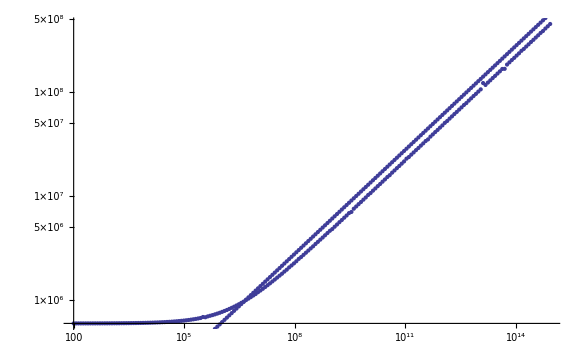

```mathematica
Show[{p1,p2}]
```

```mathematica
fun2=Normal[Series[fun,{x,0,2}]]
ne2=Integrate[fun2,{x,0,10^(8)}]
eq1=ne2==rhob/10^(10)*A0/2
(*FindRoot[eq1,{etae,Erat*2}]*)
Solve[eq1,etae]
```

(8.4393×10^12 ⅇ^etae x^2)/(2.66577993607×10^334+ⅇ^etae)

(2.8131×10^36 ⅇ^etae)/(2.66577993607×10^334+ⅇ^etae)

(2.8131×10^36 ⅇ^etae)/(2.66577993607×10^334+ⅇ^etae)==2.98726×10^27

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{etae→749.381}}

```mathematica
god=fun//.{etae->10^5}
Plot[god,{x,0,10^5}]
```

(8.4393×10^12 x^2)/(1+ⅇ^(-100000+√(592968.+x^2)))

-Graphics-

```mathematica
Integrate[fun,{x,0,etae}]
```

$Aborted

```mathematica
Integrate[x^2/(Exp[Sqrt[x^2+A^2]-B]+1),{x,0,B}]
```

$Aborted

2.15×10^6

{etae→2.15×10^6}

(8.4393×10^12 x^2)/(1+ⅇ^(-2.15×10^6+√(592968.+x^2)))

2.79577×10^31

2.98726×10^31

-0.0331133

```mathematica
ne=Integrate[fun,{x,0,Infinity}]
eq1=ne==rhob/10^(10)*A0/2
NSolve[eq1,etae]
```

∫_0^∞ (8.4393×10^12 x^2)/(1+ⅇ^(-etae+√(592968.+x^2)))ⅆx

∫_0^∞ (8.4393×10^12 x^2)/(1+ⅇ^(-etae+√(592968.+x^2)))ⅆx==2.98726×10^31

$Aborted

```mathematica
Log[10,592967.6352387434]
```

5.77303

```mathematica
(* Can actually solve for solutions directly in closed form in terms of ProductLog *)
```

```mathematica
sols=Solve[0==funmue,etae];
sol1=sols[[1,1,2]]
sol2=sols[[2,1,2]]
sol3=sols[[3,1,2]]
```

InverseFunction::ifun: Inverse functions are being used. Values may be lost for multivalued inverses.

General::stop: Further output of InverseFunction :: "ifun" will be suppressed during this calculation.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

3. ProductLog[(-9.94632×10^6-1.72275×10^7 ⅈ) ((ⅇ^(1.5008×10^10/T) rhob)/T^3)^(1/3)]

3. ProductLog[(-9.94632×10^6+1.72275×10^7 ⅈ) ((ⅇ^(1.5008×10^10/T) rhob)/T^3)^(1/3)]

3. ProductLog[1.98926×10^7 ((ⅇ^(1.5008×10^10/T) rhob)/T^3)^(1/3)]

```mathematica
(* one solution gives real answer *)
```

```mathematica
(* load constants *)
```

```mathematica
consts={rhob->1.0``40*10^(5),T->1``40*10^4}
Get["C:\\Documents and Settings\\jon\\My Documents\\Super Documents\\math\\astronomy_constants.m"];
kb*T//.consts
```

{rhob→100000.,T→10000.}

1.3807×10^-12

```mathematica
(* evaluate closed-form solutions for difficult regime *)
```

```mathematica
sols//.consts
```

{{etae→60043.-6.28287 ⅈ},{etae→60043.+6.28287 ⅈ},{etae→60043.}}

```mathematica
(* pick real solution *)
```

```mathematica
realsol=sol3
```

3. ProductLog[1.98926×10^7 ((ⅇ^(1.5008×10^10/T) rhob)/T^3)^(1/3)]

```mathematica
asymp=Normal[Series[realsol,{T,0,0}]]
```

1/(Log[1.98926×10^7 ((ⅇ^(1.5008×10^10/T) rhob)/T^3)^(1/3)]^3)(3. Log[1.98926×10^7 ((ⅇ^(1.5008×10^10/T) rhob)/T^3)^(1/3)]^4+3. Log[Log[1.98926×10^7 ((ⅇ^(1.5008×10^10/T) rhob)/T^3)^(1/3)]]-3. Log[1.98926×10^7 ((ⅇ^(1.5008×10^10/T) rhob)/T^3)^(1/3)] Log[Log[1.98926×10^7 ((ⅇ^(1.5008×10^10/T) rhob)/T^3)^(1/3)]]+3. Log[1.98926×10^7 ((ⅇ^(1.5008×10^10/T) rhob)/T^3)^(1/3)]^2 Log[Log[1.98926×10^7 ((ⅇ^(1.5008×10^10/T) rhob)/T^3)^(1/3)]]-3. Log[1.98926×10^7 ((ⅇ^(1.5008×10^10/T) rhob)/T^3)^(1/3)]^3 Log[Log[1.98926×10^7 ((ⅇ^(1.5008×10^10/T) rhob)/T^3)^(1/3)]]-4.5 Log[Log[1.98926×10^7 ((ⅇ^(1.5008×10^10/T) rhob)/T^3)^(1/3)]]^2+1.5 Log[1.98926×10^7 ((ⅇ^(1.5008×10^10/T) rhob)/T^3)^(1/3)] Log[Log[1.98926×10^7 ((ⅇ^(1.5008×10^10/T) rhob)/T^3)^(1/3)]]^2+1. Log[Log[1.98926×10^7 ((ⅇ^(1.5008×10^10/T) rhob)/T^3)^(1/3)]]^3)

```mathematica
(* try asymptotic solution *)
```

```mathematica
asymp//.consts
```

60043.

```mathematica
(* works in Mathematica 6.0, but not 5.1 *)
```

```mathematica
(* prepare to solve using FindRoot *)
```

```mathematica
myeq1=0==(funmue//.consts)
```

0==5.97864×10^28 ⅇ^(7.2427×10^11 (2.07215×10^-6-1.3807×10^-12 etae))-2.81294×10^12 etae^3

```mathematica
(* baryon+electron degeneracy *)
```

```mathematica
muedegendegen=6.628*ergPmev*(rhob/10^(13))^(2/3)//.consts
etaedegendegen=muedegendegen/(kb*T)//.consts
```

2.28759×10^-6

66273.4

```mathematica
(* try 1 temperature and tune maxiterations and precision so works *)
```

```mathematica
result=FindRoot[myeq1,{etae,1},MaxIterations->100000,WorkingPrecision->40,PrecisionGoal->5]
result[[1,2]]
(*
FindRoot[myeq2,{etae,1},MaxIterations->10000,WorkingPrecision->40]
FindRoot[myeq3,{etae,1},MaxIterations->10000,WorkingPrecision->40]
*)
```

FindRoot::precw: The precision of the argument function (0 == 5.97864×10^28\ ⅇ^7.2427×10^11\ (2.07215×10^-6 - 1.3807×10^-12\ etae) - 2.81294×10^12\ etae^3) is less than WorkingPrecision (40.).

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100000 iterations.

{etae→100000.9999999999939993692941367594201841}

100000.9999999999939993692941367594201841

```mathematica
funmueplot=funmue//.consts//.{etae->10^x}
Plot[funmueplot,{x,5,7}]
```

-2.81294×10^12 10^(3 x)+5.97864×10^28 ⅇ^(7.2427×10^11 (2.07215×10^-6-1.3807×10^-12 10^x))

-Graphics-

```mathematica
god=funmue//.{T->10^5}//.{etae->10^x,rhob->10^y}
ContourPlot[god==0,{x,3,10},{y,2,9},PlotPoints->1000]
```

-2.81294×10^15 10^(3 x)+5.97864×10^23 10^y ⅇ^(7.2427×10^10 (2.07215×10^-6-1.3807×10^-11 10^x))

```mathematica
.
```

```mathematica
(* find solution for etae for all temperatures :: only takes many iterations for low temperatures.  After about T=1E6 goes much faster :: Entire sequence of temperatures takes about 5 minutes to generate on 1.8Ghz Pentium CPU, most of time from low temperatures *)
```

```mathematica
NUM=200;
lTtable=Table[5.+i*(12-5)/(NUM-1),{i,0,NUM-1}];
etaetable=Table[0*i,{i,0,NUM-1}];
```

```mathematica
For[i=1,i<NUM,
tosolve=(funmue//.{rhob->10^(12),T->10^lTtable[[i]]});
result=FindRoot[tosolve==0,{etae,1},MaxIterations->1000000,WorkingPrecision->40];
etaetable[[i]]=result[[1,2]];
Print[i];
i++;
];
```

FindRoot::precw: The precision of the argument function (5.97864×10^35\ ⅇ^7.2427×10^10\ (2.07215×10^-6 - 1.3807×10^-11\ etae) - 2.81294×10^15\ etae^3 == 0) is less than WorkingPrecision (40.).

1

FindRoot::precw: The precision of the argument function (5.97864×10^35\ ⅇ^6.67921×10^10\ (2.07215×10^-6 - 1.49718×10^-11\ etae) - 3.58665×10^15\ etae^3 == 0) is less than WorkingPrecision (40.).

2

FindRoot::precw: The precision of the argument function (5.97864×10^35\ ⅇ^6.15955×10^10\ (2.07215×10^-6 - 1.6235×10^-11\ etae) - 4.57316×10^15\ etae^3 == 0) is less than WorkingPrecision (40.).

General::stop: Further output of FindRoot :: "precw" will be suppressed during this calculation.

3

4

5

6

7

$Aborted

```mathematica
(* make table to plot solution from non-linear equation using FindRoot *)
```

```mathematica
table2plot=Table[{10^lTtable[[i]],etaetable[[i]]},{i,1,200}];
```

```mathematica
(* get plot for asympototic solution *)
```

1/(Log[1.98923×10^11 ((ⅇ^(1.5008×10^10/T))/T^3)^(1/3)]^3)(3. Log[1.98923×10^11 ((ⅇ^(1.5008×10^10/T))/T^3)^(1/3)]^4+3. Log[Log[1.98923×10^11 ((ⅇ^(1.5008×10^10/T))/T^3)^(1/3)]]-3. Log[1.98923×10^11 ((ⅇ^(1.5008×10^10/T))/T^3)^(1/3)] Log[Log[1.98923×10^11 ((ⅇ^(1.5008×10^10/T))/T^3)^(1/3)]]+3. Log[1.98923×10^11 ((ⅇ^(1.5008×10^10/T))/T^3)^(1/3)]^2 Log[Log[1.98923×10^11 ((ⅇ^(1.5008×10^10/T))/T^3)^(1/3)]]-3. Log[1.98923×10^11 ((ⅇ^(1.5008×10^10/T))/T^3)^(1/3)]^3 Log[Log[1.98923×10^11 ((ⅇ^(1.5008×10^10/T))/T^3)^(1/3)]]-4.5 Log[Log[1.98923×10^11 ((ⅇ^(1.5008×10^10/T))/T^3)^(1/3)]]^2+1.5 Log[1.98923×10^11 ((ⅇ^(1.5008×10^10/T))/T^3)^(1/3)] Log[Log[1.98923×10^11 ((ⅇ^(1.5008×10^10/T))/T^3)^(1/3)]]^2+1. Log[Log[1.98923×10^11 ((ⅇ^(1.5008×10^10/T))/T^3)^(1/3)]]^3)

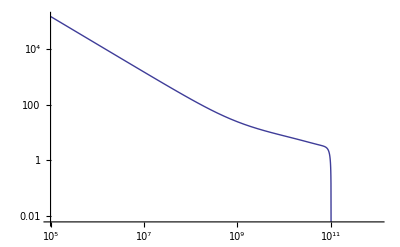

```mathematica
asympplot=asymp//.{rhob->10^(12)}
p2=LogLogPlot[asympplot,{T,10^5,10^12}]
```

1/(Log[3.77361324291657×10^21728 rhob^(1/3)]^3)(3. Log[3.77361324291657×10^21728 rhob^(1/3)]^4+3. Log[Log[3.77361324291657×10^21728 rhob^(1/3)]]-3. Log[3.77361324291657×10^21728 rhob^(1/3)] Log[Log[3.77361324291657×10^21728 rhob^(1/3)]]+3. Log[3.77361324291657×10^21728 rhob^(1/3)]^2 Log[Log[3.77361324291657×10^21728 rhob^(1/3)]]-3. Log[3.77361324291657×10^21728 rhob^(1/3)]^3 Log[Log[3.77361324291657×10^21728 rhob^(1/3)]]-4.5 Log[Log[3.77361324291657×10^21728 rhob^(1/3)]]^2+1.5 Log[3.77361324291657×10^21728 rhob^(1/3)] Log[Log[3.77361324291657×10^21728 rhob^(1/3)]]^2+1. Log[Log[3.77361324291657×10^21728 rhob^(1/3)]]^3)

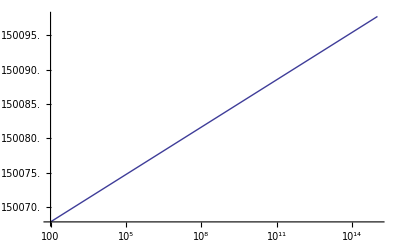

```mathematica
asympplot=asymp//.{T->10^5}
p2=LogLogPlot[asympplot,{rhob,10^2,10^15}]
```

```mathematica
it=Expand[FullSimplify[asymp,{rhob>0,T>0}]]//.{Log[(ⅇ^(5.00266040170966*^9/T) rhob^(1/3))/T]->log2,Log[(1.9892646415649775*^7 ⅇ^(5.00266040170966*^9/T) rhob^(1/3))/T]->log1}
```

3. Log[(1.98923×10^7 ⅇ^(5.00266×10^9/T) rhob^(1/3))/T]-(47.4175 Log[Log[(1.98923×10^7 ⅇ^(5.00266×10^9/T) rhob^(1/3))/T]])/(Log[(1.98923×10^7 ⅇ^(5.00266×10^9/T) rhob^(1/3))/T]^3)-(3. log2 Log[Log[(1.98923×10^7 ⅇ^(5.00266×10^9/T) rhob^(1/3))/T]])/(Log[(1.98923×10^7 ⅇ^(5.00266×10^9/T) rhob^(1/3))/T]^3)-(47.4175 Log[Log[(1.98923×10^7 ⅇ^(5.00266×10^9/T) rhob^(1/3))/T]])/Log[(1.98923×10^7 ⅇ^(5.00266×10^9/T) rhob^(1/3))/T]-(3. log2 Log[Log[(1.98923×10^7 ⅇ^(5.00266×10^9/T) rhob^(1/3))/T]])/Log[(1.98923×10^7 ⅇ^(5.00266×10^9/T) rhob^(1/3))/T]+(20.7088 Log[Log[(1.98923×10^7 ⅇ^(5.00266×10^9/T) rhob^(1/3))/T]]^2)/(Log[(1.98923×10^7 ⅇ^(5.00266×10^9/T) rhob^(1/3))/T]^3)+(1.5 log2 Log[Log[(1.98923×10^7 ⅇ^(5.00266×10^9/T) rhob^(1/3))/T]]^2)/(Log[(1.98923×10^7 ⅇ^(5.00266×10^9/T) rhob^(1/3))/T]^3)+(1. Log[Log[(1.98923×10^7 ⅇ^(5.00266×10^9/T) rhob^(1/3))/T]]^3)/(Log[(1.98923×10^7 ⅇ^(5.00266×10^9/T) rhob^(1/3))/T]^3)

```mathematica
FullSimplify[it//.{log1->Log[A*Exp[B/T]*rhob^(1/3)/T],log2->Log[Exp[B/T]*rhob^(1/3)/T]}]
```

1/(Log[(1.98923×10^7 ⅇ^(5.00266×10^9/T) rhob^(1/3))/T]^3)(3. Log[(1.98923×10^7 ⅇ^(5.00266×10^9/T) rhob^(1/3))/T]^4+Log[(1.98923×10^7 ⅇ^(5.00266×10^9/T) rhob^(1/3))/T]^2 (-47.4175-3. Log[(ⅇ^(B/T) rhob^(1/3))/T]) Log[Log[(1.98923×10^7 ⅇ^(5.00266×10^9/T) rhob^(1/3))/T]]+Log[Log[(1.98923×10^7 ⅇ^(5.00266×10^9/T) rhob^(1/3))/T]] (1. (-2.08068+Log[Log[(1.98923×10^7 ⅇ^(5.00266×10^9/T) rhob^(1/3))/T]]) (22.7894+Log[Log[(1.98923×10^7 ⅇ^(5.00266×10^9/T) rhob^(1/3))/T]])+Log[(ⅇ^(B/T) rhob^(1/3))/T] (-3.+1.5 Log[Log[(1.98923×10^7 ⅇ^(5.00266×10^9/T) rhob^(1/3))/T]])))

```mathematica
FullSimplify[it]
```

1/(Log[(1.98923×10^7 ⅇ^(5.00266×10^9/T) rhob^(1/3))/T]^3)(3. Log[(1.98923×10^7 ⅇ^(5.00266×10^9/T) rhob^(1/3))/T]^4+(-47.4175-3. log2) Log[(1.98923×10^7 ⅇ^(5.00266×10^9/T) rhob^(1/3))/T]^2 Log[Log[(1.98923×10^7 ⅇ^(5.00266×10^9/T) rhob^(1/3))/T]]+Log[Log[(1.98923×10^7 ⅇ^(5.00266×10^9/T) rhob^(1/3))/T]] (-47.4175-3. log2+Log[Log[(1.98923×10^7 ⅇ^(5.00266×10^9/T) rhob^(1/3))/T]] (20.7088+1.5 log2+1. Log[Log[(1.98923×10^7 ⅇ^(5.00266×10^9/T) rhob^(1/3))/T]])))

```mathematica
Expand[Log[(1.9892646415649775*^7 ⅇ^(5.00266040170966*^9/T) rhob^(1/3))/T],{T>0,rhob>0}]
```

Log[(1.98926×10^7 ⅇ^(5.00266×10^9/T) rhob^(1/3))/T]

```mathematica
FullSimplify[Log[A*Exp[B/T]*rhob^(1/3)/T]]
```

Log[(A ⅇ^(B/T) rhob^(1/3))/T]

```mathematica
mylog1=Log[1.9892646415649775*10^7]+Log[rhob^(1/3)]+Log[1/T]+(5.00266040170966*10^9/T)
```

16.8059+(5.00266×10^9)/T+Log[rhob^(1/3)]+Log[1/T]

```mathematica
mylog2=Log[rhob^(1/3)]+Log[1/T]+(5.00266040170966*10^9/T)
```

(5.00266×10^9)/T+Log[rhob^(1/3)]+Log[1/T]

```mathematica
mylog1//.consts
mylog2//.consts
```

20024.2

20007.4

```mathematica
FortranForm[it]
```

3.*Log((1.9892272651730984e7*E**(5.00266040170966e9/T)*rhob**0.3333333333333333)/T) - 
     -  (47.417525715975096*Log(Log((1.9892272651730984e7*E**(5.00266040170966e9/T)*rhob**0.3333333333333333)/T)))/Log((1.9892272651730984e7*E**(5.00266040170966e9/T)*rhob**0.3333333333333333)/T)**3 - 
     -  (3.*log2*Log(Log((1.9892272651730984e7*E**(5.00266040170966e9/T)*rhob**0.3333333333333333)/T)))/Log((1.9892272651730984e7*E**(5.00266040170966e9/T)*rhob**0.3333333333333333)/T)**3 - 
     -  (47.417525715975096*Log(Log((1.9892272651730984e7*E**(5.00266040170966e9/T)*rhob**0.3333333333333333)/T)))/Log((1.9892272651730984e7*E**(5.00266040170966e9/T)*rhob**0.3333333333333333)/T) - 
     -  (3.*log2*Log(Log((1.9892272651730984e7*E**(5.00266040170966e9/T)*rhob**0.3333333333333333)/T)))/Log((1.9892272651730984e7*E**(5.00266040170966e9/T)*rhob**0.3333333333333333)/T) + 
     -  (20.708762857987548*Log(Log((1.9892272651730984e7*E**(5.00266040170966e9/T)*rhob**0.3333333333333333)/T))**2)/Log((1.9892272651730984e7*E**(5.00266040170966e9/T)*rhob**0.3333333333333333)/T)**3 + 
     -  (1.5*log2*Log(Log((1.9892272651730984e7*E**(5.00266040170966e9/T)*rhob**0.3333333333333333)/T))**2)/Log((1.9892272651730984e7*E**(5.00266040170966e9/T)*rhob**0.3333333333333333)/T)**3 + 
     -  (1.*Log(Log((1.9892272651730984e7*E**(5.00266040170966e9/T)*rhob**0.3333333333333333)/T))**3)/Log((1.9892272651730984e7*E**(5.00266040170966e9/T)*rhob**0.3333333333333333)/T)**3

```mathematica
Log[(1.9892646415649775*^7 ⅇ^(5.00266040170966*^9/T) rhob^(1/3))/T]//.consts
Log[(ⅇ^(5.00266040170966*^9/T) rhob^(1/3))/T]//.consts
```

20024.228591708321715

20007.4227310138

```mathematica
(* show both FindRoot and asymptotic solutions *)
```

```mathematica
Show[{p1,p2}]
```

Show::gcomb: Could not combine the graphics objects in ….

Show[{p1,-Graphics-}]

General::unfl: Underflow occurred in computation.

General::stop: Further output of General :: "unfl" will be suppressed during this calculation.

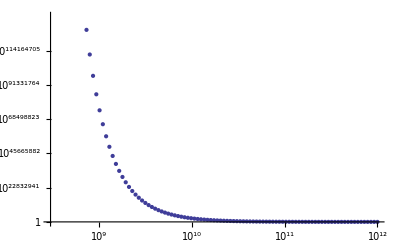

```mathematica
tablenpratio2plot=Table[{10^lTtable[[i]],1.0/Exp[(QE-etaetable[[i]])/(kb*10^lTtable[[i]])]},{i,1,200}];
p3=ListLogLogPlot[tablenpratio2plot]
```

```mathematica
i=199
myT=10^lTtable[[i]]
kb*myT
QE
myetae=etaetable[[i]]
Exp[-(QE-myetae)/(kb*myT)]
```

199

9.22198×10^11

0.000127328

2.07215×10^-6

0.5429348840151174599657011890095725838147

7.15975946576×10^1851

```mathematica
xnuc=11.33226*(rhob/10^(10))^(-3/4)*(T/10^10)^(1.125)*Exp[-8.20899/(T/10^10)]//.consts
```

4.11755188971801×10^-142611